```mathematica
(*readMe
1 - This notebook works with the cosmic chronometers. If you do not want it, drop the "CC" part in the files names and remove the chi2Hz from chi2total and chi2totalvec
2 - Calculation are independent from h but we leave h as a paramter in each of them if you which to use this code by implementing h in the chi2
*)
```

## Cosmology

```mathematica
c=299792.458;
(*Choose here the SN data you want (=1, 0 otherwise) and if you want to consider ϵ (=1) or not (=0)*)
eps=0;
Union15=1;
Union18=0;
Pantheon=0;
DESIDoveki=0;
If[Union15+Union18+Pantheon+DESIDoveki>1,Print["ALERTE: multiple supernovae data set !!!!"]];

If[Union15==1,
If[eps==0 ,
Print ["Union1.5 without ϵ"];
figureName="\\figure\\Union15CCLCDM";
smallchainname="smallchainUnion15CCLCDM";
bigchainname="bigchainUnion15CCLCDM"
,
Print ["Union1.5 with ϵ"];
figureName="\\figure\\Union15CCLCDMEps";
smallchainname="smallchainUnion15CCLCDMEps";
bigchainname="bigchainUnion15CCLCDMEps"
]
]

If[Union18==1,
If[eps==0 ,
Print ["Union1.8 without ϵ"];
figureName="\\figure\\Union18CCLCDM";
smallchainname="smallchainUnion18CCLCDM";
bigchainname="bigchainUnion18CCLCDM"
,
Print ["Union1.8 with ϵ"];
figureName="\\figure\\Union18CCLCDMEps";
smallchainname="smallchainUnion18CCLCDMEps";
bigchainname="bigchainUnion18CCLCDMEps"
]
]

If[Pantheon==1,
If[eps==0 ,
Print ["Pantheon without ϵ"];
figureName="\\figure\\PantheonCCLCDM";
smallchainname="smallchainPantheonCCLCDM";
bigchainname="bigchainPantheonCCLCDM"
,
Print ["Pantheon with ϵ"];
figureName="\\figure\\PantheonCCLCDMEps";
smallchainname="smallchainPantheonCCLCDMEps";
bigchainname="bigchainPantheonCCLCDMEps"
]
]

If[DESIDoveki==1,
If[eps==0 ,
Print ["DESIDoveki without ϵ"];
figureName="\\figure\\DESDowekiCCLCDM";
smallchainname="smallchainDESDowekiCCLCDM";
bigchainname="bigchainDESDowekiCCLCDM"
,
Print ["DESIDoveki with ϵ"];
figureName="\\figure\\DESDovekiCCLCDMEps";
smallchainname="smallchainDESDovekiCCLCDMEps";
bigchainname="bigchainDESDovekiCCLCDMEps"
]
]

(* ===================================================================== *)
(* data path *)
(* ===================================================================== *)
SetDirectory[NotebookDirectory[]];
datapath=NotebookDirectory[];
(* For SnIa data *)
SnIapath="data\\";
(* ===================================================================== *)
(* w=-1*)
(* ===================================================================== *)
HubbleCompiled[om_,α_,β_,h_]:=Compile[{{Np,_Real}},Sqrt[10000 h^2 om Exp[-3 Np]+10000 h^2 (1-om)],RuntimeAttributes->{Listable}];
(* =====================================================================*)(*Build interpolation function*)(* =====================================================================*)BuildGInterp[om_?NumberQ,α_?NumberQ,β_?NumberQ,h_?NumberQ,Nmin_,nsteps_: 1000]:=Module[{Hc,Ngrid,integrand,step,cumInt,total,Gvals},Hc=HubbleCompiled[om,α,β,h];
Ngrid=N[Subdivide[Nmin,0,nsteps]];
integrand=Exp[-Ngrid]/Hc[Ngrid];
step=-Nmin/nsteps;
cumInt=Prepend[Accumulate[(integrand[[1;;-2]]+integrand[[2;;]])/2*step],0.];
total=Last[cumInt];
Gvals=total-cumInt;(*G(Ngrid[[i]])*)
Interpolation[Transpose[{Ngrid,Gvals}],InterpolationOrder->3]];

(* =====================================================================*)
(*Distances using Ginterp*)
(* =====================================================================*)
DMfast[zList_?(VectorQ[#,NumberQ]&),Ginterp_]:=c*(Ginterp[-Log[1.+#]]&/@zList);
DMfast[z_?NumberQ,Ginterp_]:=First[DMfast[{z},Ginterp]];

DLfast[zList_?(VectorQ[#,NumberQ]&),Ginterp_]:=(1+zList)*DMfast[zList,Ginterp];
DLfast[z_?NumberQ,Ginterp_]:=First[DLfast[{z},Ginterp]];

DHfast[zList_?(VectorQ[#,NumberQ]&),Hc_]:=c/Hc[-Log[1.+zList]];
DHfast[z_?NumberQ,Hc_]:=First[DHfast[{z},Hc]];

DVfast[zList_?(VectorQ[#,NumberQ]&),Ginterp_,Hc_]:=Module[{DMList,HzList},DMList=DMfast[zList,Ginterp];
HzList=Hc[-Log[1.+zList]];
(c*zList*DMList^2/HzList)^(1/3)];
DVfast[z_?NumberQ,Ginterp_,Hc_]:=First[DVfast[{z},Ginterp,Hc]];

(* ===================================================================== *)
(*Data BAO*)
(* ===================================================================== *)
databao={{0.29500000,7.94167639,"DV_over_rs"},{0.51000000,13.58758434,"DM_over_rs"},{0.51000000,21.86294686,"DH_over_rs"},{0.70600000,17.35069094,"DM_over_rs"},{0.70600000,19.45534918,"DH_over_rs"},{0.93400000,21.57563956,"DM_over_rs"},{0.93400000,17.64149464,"DH_over_rs"},{1.32100000,27.60085612,"DM_over_rs"},{1.32100000,14.17602155,"DH_over_rs"},{1.48400000,30.51190063,"DM_over_rs"},{1.48400000,12.81699964,"DH_over_rs"},{2.33,8.631545674846294,"DH_over_rs"},{2.33,38.988973961958784,"DM_over_rs"}};

dataCov={5.78998687*10^(-3),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,2.83473742*10^(-2),-3.26062007*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-3.26062007*10^(-2),1.83928040*10^(-1),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,3.23752442*10^(-2),-2.37445646*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-2.37445646*10^(-2),1.11469198*10^(-1),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,2.61732816*10^(-2),-1.12938006*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-1.12938006*10^(-2),4.04183878*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,1.05336516*10^(-1),-2.90308418*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-2.90308418*10^(-2),5.04233092*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,5.83020277*10^(-1),-1.95215562*10^(-1),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-1.95215562*10^(-1),2.68336193*10^(-1),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,1.02136194*10^(-2),-2.31395216*10^(-2),0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,0.00000000,-2.31395216*10^(-2),2.82685779*10^(-1)};
matDataCov=Partition[dataCov,Sqrt[Length[dataCov]]];
Cijbaoinv=Inverse[matDataCov];
(* ===================================================================== *)
(*Data SN*)
(* ===================================================================== *)
If[Union15==1,
dataSN="\\Union31\\mu_mat_union3_cosmo=2_mu.fits";
Print["Use data: ",dataSN ];
dataSupernova=Import[SnIapath<>dataSN,"Data"][[1]];
InvCovTotal=dataSupernova[[2;; ,2;;]];
]
If[Union18==1,
dataSN="\\Union31\\mu_mat_union3.1_UNITY1.8_template_cosmo=2_0_mu.fits";
Print["Use data: ",dataSN ];
dataSupernova=Import[SnIapath<>dataSN,"Data"][[1]];
InvCovTotal=dataSupernova[[2;; ,2;;]];
]
If[Pantheon==1,
dataSN="\\Pantheon\\Pantheon+SH0ES.dat";
Print["Use data: ",dataSN ];
dataPanth=Import[SnIapath<>dataSN,"Table"];
positions1=Flatten@Position[dataPanth[[All,3]],z_/;z<0.01];
(*Get the position of the Cepheid calibrators*)
positions2=Flatten@Position[dataPanth[[All,14]],z_/;z==1];
positions=DeleteDuplicates[Join[positions1,positions2]];
(*1580 SN (+1 ligne) such as z>0.01 and without calibrators*)
newDataPanth=Delete[dataPanth,List/@positions];
ndatPanth=Length[newDataPanth]-1;
filecovs="Pantheon+SH0ES_STAT+SYS.zip";
Dij0=Import[SnIapath<>"\\Pantheon\\"<>filecovs,{"ZIP","Pantheon+SH0ES_STAT+SYS.cov","List"}];
(*Covariance matrix for all the Pantheon SN*)
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
(*Lines and columns to remove in the covariance matrix*)
posRemCov=positions-Table[1,{i,1,Length[positions]}];
(*Element to keep in the covariance matrix*)
keep=Complement[Range[Length[Dij]],posRemCov];
(*Covariance matrix for 1580 Pantheon SN*)
newDij=Dij[[keep,keep]];
InvCovTotal=Inverse[newDij];
]

If[DESIDoveki==1,
dataSN="\\DESI\\DES-Dovekie_HD.csv";
Print["Use data: ",dataSN ];
dataDESISN=Import[SnIapath<>dataSN,"Table"];
ndatDESISN=Length[dataDESISN]-9;
InvCovTotal=Import[SnIapath<>"\\DESI\\InvCovTotal.csv"];
InvCovTotal=Developer`ToPackedArray[N[InvCovTotal]];
];

(* ===================================================================== *)
(*Data H (https://gitlab.com/mmoresco/CCcovariance/-/tree/master/data)*)
(* ===================================================================== *)
dataHz=Drop[Import[datapath<>"\\data\\CC\\HzTable_MM_BC03.dat","CSV"],1];
Get[datapath<>"\\data\\CC\\HzTableCovariance.txt"];
invDataHzCov=Inverse[covTotal];
(* =====================================================================*)
(*Chi2*)
(* =====================================================================*)
Clear[tBAO,dBAO,vecbao]
tBAO[om_,α_,β_,h_,Ginterp_,Hc_]:=Table[If[databao[[i,3]]=="DV_over_rs",100 h/c DVfast[databao[[i,1]],Ginterp,Hc],If[databao[[i,3]]=="DM_over_rs",100 h/c DMfast[databao[[i,1]],Ginterp],If[databao[[i,3]]=="DH_over_rs",100 h/c DHfast[databao[[i,1]],Hc]]]],{i,1,Length[databao]}];

dBAO[om_,α_,β_,h_]:=Table[databao[[i,2]],{i,1,Length[databao]}];
vecbao[om_?NumberQ,α_?NumberQ,β_?NumberQ,h_?NumberQ,Ginterp_,Hc_]:=Module[{bstar=0,tBAOval,dBAOval},dBAOval=dBAO[om,α,β,h];
tBAOval=tBAO[om,α,β,h,Ginterp,Hc];
(*bstar is c/(H0 rd)*)
bstar=tBAOval.Cijbaoinv.dBAOval/(tBAOval.Cijbaoinv.tBAOval);
Return[dBAOval-bstar tBAOval]]
getbstar[om_?NumberQ,α_?NumberQ,β_?NumberQ,h_?NumberQ,Ginterp_,Hc_]:=Module[{bstar=0,tBAOval,dBAOval},
dBAOval=dBAO[om,α,β,h];
tBAOval=tBAO[om,α,β,h,Ginterp,Hc];
(*bstar is c/(H0 rd)*)
bstar=tBAOval.Cijbaoinv.dBAOval/(tBAOval.Cijbaoinv.tBAOval);
Return[{bstar,1/Sqrt[tBAOval.Cijbaoinv.tBAOval]}]]
chi2bao[om_,α_,β_,h_,Ginterp_,Hc_]:=Module[{v},
v=vecbao[om,α,β,h,Ginterp,Hc];
v.Cijbaoinv.v]

If[Union15==1 || Union18==1,
mag=dataSupernova[[2;; ,1]];
redshift=dataSupernova[[1,2;;]];
ndatSupernova=Length[redshift];
u=ConstantArray[1.,ndatSupernova];
Ciu=InvCovTotal.u;
(*constant,ne dépend pas des paramètres*)
uCiu=u.Ciu;
chi2SN[om_?NumberQ,α_?NumberQ,β_?NumberQ,ε_?NumberQ,h_?NumberQ,Ginterp_]:=Module[{dLList,d,Cid,uCid},
dLList=DLfast[redshift,Ginterp];
d=mag-5*Log10[(100 h)/c*dLList*(1+redshift)^ε];
Cid=InvCovTotal.d;
uCid=u.Cid;
d.Cid-uCid^2/uCiu];
];
If[Pantheon==1,
mag=Table[Part[newDataPanth,i+1,9],{i,1,Length[newDataPanth]-1}];
redshift=Table[Part[newDataPanth,i+1,3],{i,1,Length[newDataPanth]-1}];
u = ConstantArray[1., ndatPanth];
Ciu = InvCovTotal.u;
uCiu=u.Ciu;
chi2SN[om_?NumberQ,α_?NumberQ,β_?NumberQ,ε_?NumberQ,h_?NumberQ,Ginterp_]:=Module[{dLList,d,Cid,uCid},
dLList=DLfast[redshift,Ginterp];
d=mag-5*Log10[(100 h)/c*dLList*(1+redshift)^ε];
Cid=InvCovTotal.d;
uCid=u.Cid;
d.Cid-uCid^2/uCiu];
];
If[DESIDoveki==1,
mag=Table[dataDESISN[[9+i,6]],{i,1,ndatDESISN}];
redshift=Table[dataDESISN[[9+i,4]],{i,1,ndatDESISN}];
u = ConstantArray[1., ndatDESISN];
Ciu = InvCovTotal.u;
uCiu=u.Ciu;
chi2SN[om_?NumberQ,α_?NumberQ,β_?NumberQ,ε_?NumberQ,h_?NumberQ,Ginterp_]:=Module[{dLList,d,Cid,uCid},
dLList=DLfast[redshift,Ginterp];
d=mag-5*Log10[(100 h)/c*dLList*(1+redshift)^ε];
Cid=InvCovTotal.d;
uCid=u.Cid;
d.Cid-uCid^2/uCiu];
];

magH=Table[Part[dataHz,i,2],{i,1,Length[dataHz]}];
sigmaH=Table[Part[dataHz,i,3],{i,1,Length[dataHz]}];
redshiftH=Table[Part[dataHz,i,1],{i,1,Length[dataHz]}];
chi2Hz[om_?NumberQ,α_?NumberQ,β_?NumberQ,h_?NumberQ,Hc_]:=Module[{hTheo,A,B,rm},
hTheo=(1/(100 h))*Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
rm=magH-B/A hTheo;
Return[rm.invDataHzCov.rm]]

chi2total[om_?NumberQ,α_?NumberQ,β_?NumberQ,ε_?NumberQ,h_?NumberQ]:=Module[{Hc,Ginterp,Nmin},
Hc=HubbleCompiled[om,α,β,h];
Nmin=-Log[1.+Max[Join[redshift,redshiftH,databao[[All,1]]]]]-0.1;
Ginterp=BuildGInterp[om,α,β,h,Nmin];
chi2bao[om,α,β,h,Ginterp,Hc]+chi2SN[om,α,β,ε,h,Ginterp]+chi2Hz[om,α,β,h,Hc]]

chi2totalvec[om_?NumberQ,α_?NumberQ,β_?NumberQ,ε_?NumberQ,h_?NumberQ]:=Module[{Hc,Ginterp,Nmin},
Hc=HubbleCompiled[om,α,β,h];
Nmin=-Log[1.+Max[Join[redshift,databao[[All,1]]]]]-0.1;
Ginterp=BuildGInterp[om,α,β,h,Nmin];
{chi2bao[om,α,β,h,Ginterp,Hc],chi2SN[om,α,β,ε,h,Ginterp],chi2Hz[om,α,β,h,Hc]}]
```

Union1.5 without ϵ

\Chain\bigchainUnion15CCLCDM

Use data: \Union31\mu_mat_union3_cosmo=2_mu.fits

```mathematica
testSol={0.3048011851378613,-1,0,0.,1};
testH={h->Part[testSol,5]};
test={om->Part[testSol,1],α->Part[testSol,2],β->Part[testSol,3],ϵ->Part[testSol,4]};
chi2total[om,α,β,ϵ,h]/.test/.testH
```

45.0711

```mathematica
chi2totalvec[om,α,β,ϵ ,h]/.test/.testH
```

{10.977,27.8535,6.24061}

```mathematica
FindMinimum[
chi2total[om,-1,0,0,0.01],{om,0.1,0.5}]
```

{45.0622,{om→0.304015}}

```mathematica
getH[om_?NumberQ,h_?NumberQ,Hc_]:=Module[{hTheo,A,B,rm},
hTheo=(1/(100 h))*Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
rm=magH-B/A hTheo;
Print["Best H0=",B/A," erreur σ=", 1/Sqrt[A]];
]
whatH[om_?NumberQ,ε_?NumberQ,h_?NumberQ]:=Module[{Hc,Ginterp,Nmin},
Hc=HubbleCompiled[om,α,β,h];
Nmin=-Log[1.+Max[Join[redshift,redshiftH,databao[[All,1]]]]]-0.1;
Ginterp=BuildGInterp[om,α,β,h,Nmin];
getH[om,h,Hc]]
testSol={om->0.3216006965705047,ϵ->0};
testSol={om->0.321,ϵ->0};
whatH[om,ϵ,1]/.testSol
```

Best H0=67.6886 erreur σ=3.89654

## MCMC

```mathematica
(* This is the jump function // Proposes the next point *)
jumpfunc[point_,s_]:=point+RandomVariate[NormalDistribution[0,s],Length[point]]
jumpfuncmat[point_,cijtest_]:=RandomVariate[MultinormalDistribution[point,cijtest]]
(* Δχ^2 for 2 params, up to 3σ *)
dx2=Table[2 InverseGammaRegularized[Nn/2,1-Erf[xσ/(√2)]]/.Nn->2//N,{xσ,1,3}];
mysymmetrize[Cij_]:=(Cij+Transpose[Cij])/2;
(* Contours+color from the MCMC // Uses ConvexHull // Advanced++ *)
Needs["ComputationalGeometry`"];
Off[CompiledFunction::cflist];
Confid2D[data_List,color_,inter_]:=Module[{cv,cv1,cv2,qq},cv=ConvexHull[data,AllPoints->True];cv1=data[[#]]&/@cv;cv2=Join[cv1,{cv1[[1]],cv1[[2]]}];qq=Show[Graphics[{color,FilledCurve[BSplineCurve[cv2,SplineDegree->inter,SplineKnots->"Unclamped"]],Antialiasing->True}],Frame->True];qq]
normalize[bins_,counts_]:=counts/Max[counts]
(* Convergence diagnostics *)
Rstatistic[chain_,param_,burnin_]:=Module[{n,m,W,B,Rminus1},
m=chain//Length;
n=Table[chain[[i,burnin;;-1,1,param]]//Length,{i,1,m}]//Mean;
W=Mean[Table[Variance[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
B=n Variance[Table[Mean[chain[[j,burnin;;-1,1,param]]],{j,1,m}]];
Rminus1=√((1-1/n)+1/n B/W)-1]
(* Utils *)
time[dt1_]:=Which[dt1<60,ToString[dt1]<>" secs",60≤dt1<1000,ToString[dt1/60.]<>" mins",1000≤dt1,ToString[dt1/3600.]<>" hrs"]
(* Triangle plot *)
(* Some code borrowed from 
"https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately";*)
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
plempty[{left_,right_}]:=Plot[0,{x,-1,1},Frame->True,Axes->False,PlotStyle->White,FrameStyle->{{left,right},{White,White}},FrameTicks->None];
pleint=plempty[{Automatic,White}];
pleout=plempty[{White,White}];
```

## Initial MCMC

```mathematica
(* Do a small MCMC *)
Clear[h];
If[eps==0,
(*Union*)
priors={{0.1,0.5}};
jumpsize={0.0001};
chi2[om_]:=Module[{},
chi2total[om,-1,0,0,1]
]
,
(*Union*)
priors={{0.1,0.5},{-0.8,0.8}};
jumpsize={0.0001,0.001};
chi2[om_,ϵ_]:=Module[{},
chi2total[om,-1,0,ϵ,1]
]
]
(*om,α,β,h*)
initMCMC={om->0.30421811409942856};
If[eps==0,initpoint={om}/.initMCMC,initpoint={om,ϵ}/.initMCMC;]
For[r=0,r≤0(*200*),
step=0;
t1=AbsoluteTime[];
totalsteps=500;
Dynamic[step];
currentpoint=initpoint;
chi2current=chi2@@currentpoint;
smallchain={};
While[step<totalsteps+1,
(
proposedpoint=jumpfuncmat[currentpoint,DiagonalMatrix[jumpsize]^2];
chi2prop=chi2@@proposedpoint;
jumpprob=Exp[-(chi2prop-chi2current)/2];
If[(RandomReal[]≤Min[{1,jumpprob}])&&(And@@IntervalMemberQ[Interval@@priors,proposedpoint]),currentpoint=proposedpoint;chi2current=chi2prop;  AppendTo[smallchain,{currentpoint,chi2current}];,currentpoint=currentpoint;];
);
step++];
Print["Round= ",r," Time needed (secs): ",AbsoluteTime[]-t1];
Print[chi2min=Min[smallchain[[All,2]]]]; 
tmpsc=smallchain[[Position[smallchain,chi2min][[1,1]]]][[1]];
Print[tmpsc];
initpoint=tmpsc;
 ,r++]
```

{0.304218}

Round= 1 Time needed (secs): 4.1412616

1400.33

{0.304229}

Round= 2 Time needed (secs): 4.1570574

1400.33

{0.304097}

Round= 3 Time needed (secs): 4.1641578

1400.33

{0.304225}

Round= 4 Time needed (secs): 4.1595203

1400.33

{0.304231}

Round= 5 Time needed (secs): 4.1326616

1400.33

{0.304211}

Round= 6 Time needed (secs): 4.1601613

1400.33

{0.304215}

```mathematica
Length[smallchain]
```

501

```mathematica
(* Save the chain in zip format to save space *)
Export[smallchainname<>".zip",{smallchainname<>".m"->smallchain}];
```

```mathematica
(* Read in the chain // for postprocessing etc *)
smallchain=Import[smallchainname<>".zip",smallchainname<>".m"];
```

```mathematica
(* Best-fit from the MCMC *)
Length[smallchain]
chi2min=Min[smallchain[[All,2]]]
bf=smallchain[[Position[smallchain,chi2min][[1,1]]]][[1]]
```

501

1400.33

{0.304215}

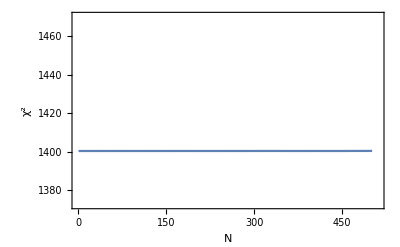

```mathematica
(* χ^2 plot *)
ListPlot[smallchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[smallchain[[All,2]]]},chi2min{0.98,1.05}},Frame->True,FrameLabel->{"N","χ^2"}]
```

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[smallchain];
burnin=Round[0.1*chlen];
Cijchain0=Covariance[smallchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain0]
SymmetricMatrixQ[Cijchain0]
Cijchain0//Diagonal//Sqrt
```

{{2.22753×10^-7}}

True

True

{0.000471967}

## Main MCMC

```mathematica
(* Read in the chain // for postprocessing etc *)
smallchain=Import[smallchainname<>".zip",smallchainname<>".m"];
```

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[smallchain];
burnin=Round[0.1*chlen];
Cijchain0=Covariance[smallchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain0]
SymmetricMatrixQ[Cijchain0]
Cijchain0//Diagonal//Sqrt
```

{{2.22753×10^-7}}

True

True

{0.000471967}

```mathematica
{Min[smallchain[[All,2]]],
smallchain[[Position[smallchain,Min[smallchain[[All,2]]]][[1,1]]]][[1]]}
chi2min=Min[smallchain[[All,2]]]
```

{1400.33,{0.304215}}

1400.33

```mathematica
(* Do the MCMC *)
If[eps==0,
(*Union*)
priors={{0.1,0.5}};
chi2[om_]:=Module[{},
chi2total[om,-1,0,0,1]
]
,
(*Union*)
priors={{0.1,0.5},{-0.8,0.8}};
chi2[om_,ϵ_]:=Module[{},
chi2total[om,-1,0,ϵ,1]
]
]
compteur=0;
step=0;
t1=AbsoluteTime[];
totalsteps=(*700000*)500000;
initMCMC={om->0.30421811409942856};
If[eps==0,initpoint={om}/.initMCMC;,initpoint={om,ϵ}/.initMCMC;]
currentpoint=initpoint;
chi2current=chi2@@currentpoint;
bigchain={};
ProgressIndicator[Dynamic[step],{0,totalsteps}]
While[step<totalsteps+1,
(
If[Mod[step,10000]==0,Print[Length[bigchain]];Export[bigchainname<>ToString[compteur]<>".zip",{bigchainname<>".m"->bigchain}];compteur++;bigchain={};];
proposedpoint=jumpfuncmat[currentpoint,Cijchain0];
chi2prop=chi2@@proposedpoint;
jumpprob=Exp[-(chi2prop-chi2current)/2];
If[(RandomReal[]≤Min[{1,jumpprob}])&&(And@@Table[IntervalMemberQ[Interval@priors[[i]],proposedpoint[[i]]],{i,1,Length[priors]}]),currentpoint=proposedpoint;chi2current=chi2prop;AppendTo[bigchain,{currentpoint,chi2current}];,currentpoint=currentpoint;];
);
step++]
  t["Time needed (secs): ",AbsoluteTime[]-t1]
```

{0.304218}

0

9793

9814

9812

9817

9818

9816

9809

9855

9855

9798

9816

9851

9845

9748

9760

9833

9802

9742

9797

9815

9795

9798

9795

9860

9843

9788

9821

9753

9798

9796

9853

9794

9828

9815

9771

9811

9832

9852

9806

9772

9836

9838

9814

9807

9808

9842

9802

9807

9803

9819

t[Time needed (secs): ,4157.3123985]

```mathematica
(* Save the chain in zip format to save space *)
bigchain={};
For[i=0,i≤ 50,
tmp=Import[bigchainname<>ToString[i]<>".zip",bigchainname<>".m"];
bigchain=Join[bigchain,tmp];
i++]
Export[bigchainname<>".zip",{bigchainname<>".m"->bigchain}];
```

```mathematica
bigchainname
```

bigchainPantheonLCDM

```mathematica
(* χ^2 plot *)
ListPlot[bigchain[[All,2]],Joined->True,PlotRange->{{0,1.02Length[bigchain[[All,2]]]},chi2min{0.98,1.05}},Frame->True,FrameLabel->{"N","χ^2"}]
```

-Graphics-

```mathematica
(* Cov. Matrix directly from the chain *)
chlen=Length[bigchain];
burnin=Round[0.01*chlen];
Cijchain=Covariance[bigchain[[All,1,All]][[burnin;;-1]]]
PositiveDefiniteMatrixQ[Cijchain]
SymmetricMatrixQ[Cijchain]
Cijchain//Diagonal//Sqrt
```

{{0.0000584027}}

True

True

{0.00764216}

## MCMC Plots

```mathematica
(* Set the initial priors *)
If[eps==0,
(* The parameters of the chains as they will appear in the plot *)
params={"Ω_m"};
,
params={"Ω_m","ϵ"};
]
nparams=params//Length;
```

```mathematica
(* Read in the chain // for postprocessing etc *)
Print["Big chain name is ",bigchainname]
bigchain=Import[bigchainname<>".zip",bigchainname<>".m"];
```

Big chain name is bigchainPantheonLCDMEps

```mathematica
(* Best-fit from the MCMC *)
chi2min=Min[bigchain[[All,2]]]
bf=bigchain[[Position[bigchain,chi2min][[1,1]]]][[1]]
chi2totalvec[Part[bf,1],-1,1,0,1]
```

1397.44

{0.297517,-0.0283607}

{10.2711,1390.78,115.66}

```mathematica
(* Mean values from the MCMC *)
median=bigchain[[All,1]]//Mean
(*Erreur si symétrique*)
bigchain[[All,1]]//StandardDeviation
(*Erreur (lower, upper) si non symétrique, intervalle à 68%*)
tmp=Quantile[bigchain[[All,1]],{0.16,0.84}];
Table[{median[[i]]-tmp[[i,1]],tmp[[i,2]]-median[[i]]},{i,1,Length[median]}]
```

{0.297867,-0.028341}

{0.00861555,0.0162201}

{{0.00869388,0.00860618},{0.0161003,0.0160794}}

```mathematica
Clear[mcmcchain,mcmcchain,def,fontsize,ndivs,nmax,lims,divs,ranges,pl1d,pl2d,tab,allplots]
mcmcchain=bigchain;
```

```mathematica
(* Calculate the ranges of the plots and number of ticks (default ndivs+1). Set the fontsize. *)
fontsize=12;
ndivs=3;
nmax=Length[params];
lims=Table[{Min[mcmcchain[[All,1,i]]],Max[mcmcchain[[All,1,i]]]},{i,1,nmax}]
divs=Table[FindDivisions[lims[[i]],ndivs]//N,{i,1,nmax}];
ranges=lims/.{x_,y_}->{ x-0. Abs[x],y+0. Abs[y]};
```

{{0.264215,0.337975},{-0.0974802,0.0470927}}

```mathematica
(*Exceptions table: parameter indices ->{targetCount,minCount,maxCount}*)
(*tickOverrides=<|2->{2,2,3,0.12},3->{2,3,3,0.12}|>;: indicate that on the second column, we would like 2 ticks with a minimum of two, a maximum of 3 and an enlarged marge of 12%, etc. *)
tickOverrides=<|1->{3,2,4,0.12}|>;

(*Function Fonction for thicks without labels*)
blankTicks[div_List]:=Transpose[{div,Table["",{Length[div]}]}];
getFormatTicks[i_]:=Module[{result},result=Check[If[KeyExistsQ[tickOverrides,i],formatTicks[ranges[[i]],Sequence@@tickOverrides[i]],formatTicks[ranges[[i]]]],$Failed];
If[MatchQ[result,{{_?NumericQ,_}..}]&&Length[result]>=2,result,Automatic]];

(*Find a round step (1,2,2.5,ou 5 x 10^n) near the ideal step to get targetCount graduations*)niceStep0[span_,count_]:=Module[{roughStep,mag,residual,niceMultiples,bestMult},roughStep=Max[span/(count-1),10^-8];
mag=10^Floor[Log10[roughStep]];
residual=roughStep/mag;
niceMultiples={1,2,2.5,5,10};
bestMult=First[SortBy[niceMultiples,Abs[#-residual]&]];
bestMult*mag];

niceTicks[range_List,targetCount_Integer: 3,minCount_Integer: 2,maxCount_Integer: 6,marginFrac_: 0.02]:=Module[{span=range[[2]]-range[[1]],margin,lo,hi,tryCounts,results,valid,best},margin=marginFrac*span;
lo=range[[1]]+margin;
hi=range[[2]]-margin;
tryCounts=DeleteDuplicates[Flatten[{targetCount,Range[minCount,maxCount]}]];
results=Table[Module[{step,ticks},step=niceStep0[span,c];
ticks=Range[Ceiling[lo/step]*step,hi,step];
{c,Length[ticks],ticks}],{c,tryCounts}];
valid=Select[results,minCount≤#[[2]]≤maxCount&];
If[valid==={},Subdivide[lo,hi,minCount-1],best=First[SortBy[valid,Abs[#[[1]]-targetCount]&]];
best[[3]]]];

tickLabel[x_,d_Integer]:=NumberForm[N[x],{Infinity,d},NumberPadding->{"","0"}];

tickLabelString[x_,d_Integer]:=ToString[tickLabel[x,d]];

minDecimalsForUniqueness[div_List]:=Module[{d=1,labels},While[d≤6,labels=tickLabelString[#,d]&/@div;
If[Length[DeleteDuplicates[labels]]==Length[div],Return[d]];
d++];
d];

formatTicks[range_List,targetCount_Integer: 3,minCount_Integer: 2,maxCount_Integer: 6,marginFrac_: 0.02]:=Module[{ticks,d},ticks=niceTicks[range,targetCount,minCount,maxCount,marginFrac];
d=minDecimalsForUniqueness[ticks];
{#,tickLabel[#,d]}&/@ticks]


pl1d[i_]:=SmoothHistogram[mcmcchain[[All,1,i]],Automatic,"PDF",Frame->True,PlotRange->{ranges[[i]],All},AspectRatio->1,FrameLabel->{If[i==nmax,params[[i]],None],None},FrameTicks->{{None,None},{If[i==nmax,getFormatTicks[i],blankTicks[divs[[i]]]],blankTicks[divs[[i]]]}},BaseStyle->FontSize->fontsize,Axes->False,FrameStyle->Black,PlotStyle->Black];

pl2d[i_,j_]:=Module[{datapl,skd,pdf,cons,cenp},datapl=mcmcchain[[All,1,{i,j}]];
skd=SmoothKernelDistribution[datapl];
pdf=PDF[skd,datapl];
cons=Quantile[pdf,1-Erf[{1,2,3}/Sqrt[2]]//N];
cenp=datapl//Mean;
ContourPlot[PDF[skd,{a,b}],{a,ranges[[i,1]],ranges[[i,2]]},{b,ranges[[j,1]],ranges[[j,2]]},Contours->cons,ContourShading->{White,Hue[0.6,0.5,0.8],Hue[0.55,0.5,0.8],Hue[0.5,0.5,0.9]},FrameLabel->{If[j==nmax,params[[i]],None],If[i==1,params[[j]],None]},FrameTicks->{{If[i==1,getFormatTicks[j],blankTicks[divs[[j]]]],blankTicks[divs[[j]]]},{If[j==nmax,getFormatTicks[i],blankTicks[divs[[i]]]],blankTicks[divs[[i]]]}},BaseStyle->FontSize->fontsize,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{Black,Point[cenp]}}]];

tab[i_,j_]:=Which[i==j,pl1d[i],i<j,pl2d[i,j],i==j+1,pleint,True,pleout];
```

```mathematica
(* Create the plots *)
allplots=Table[tab[i,j],{j,1,nmax},{i,1,nmax}];
```

```mathematica
Print["Result for ", bigchainname, " with ϵ=",eps," and data in ",dataSN]
triangleLCDM=Rasterize[Show[plotGrid[allplots,500,500,ImagePadding->45]],RasterSize->2000,ImageSize->600]
```

Result for bigchainPantheonLCDMEps with ϵ=1 and data in \Pantheon\Pantheon+SH0ES.dat

-Graphics-

```mathematica
Export[datapath<>figureName<>"CP.pdf",triangleLCDM]
```

C:\Users\gpp\Documents\DDRFit\\figure\PantheonLCDMEpsCP.pdf

## H0 and rd without ϵ

```mathematica
bigchainname
```

bigchainUnion15CCLCDM

```mathematica
(* Read in the chain*)
bigchain=Import[bigchainname<>".zip",bigchainname<>".m"];
```

```mathematica
bestchi2=
```

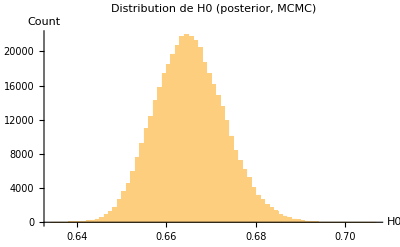

-Graphics-

```mathematica
getH0core[om_?NumberQ]:=Module[{Hc,hTheo,A,B},Hc=HubbleCompiled[om,-1,0,1.];
hTheo=Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
{B/A,1/Sqrt[A]}]

paramSamples=bigchain[[All,1]];   
chi2Samples=bigchain[[All,2]];

nBurn=Round[0.1*Length[paramSamples]];
paramSamples=paramSamples[[nBurn+1;;]];
chi2Samples=chi2Samples[[nBurn+1;;]];

(*----H0 for each point----*)
resultsChain=Apply[getH0core,paramSamples,{1}];
H0samples=resultsChain[[All,1]];
sigmaCovSamp=resultsChain[[All,2]];

{p16,p50,p84}=Quantile[H0samples,{0.16,0.5,0.84}];
sigmaPlus=p84-p50;
sigmaMinus=p50-p16;

sigmaCovMean=Mean[sigmaCovSamp];

sigmaTotalPlus=Sqrt[sigmaPlus^2+sigmaCovMean^2];
sigmaTotalMinus=Sqrt[sigmaMinus^2+sigmaCovMean^2];

Print["H0 = ",p50," +",sigmaTotalPlus," -",sigmaTotalMinus];
Print["  (erreur chaines seule: +",sigmaPlus," -",sigmaMinus,", sigma_cov moyen (CC) = ",sigmaCovMean,")"];

bestFitIdx=First@Ordering[chi2Samples,1];
getH0core[om]/.bestchi2;
Print["(H0,σ) (Best fit of FindMinimum)=",%];
Print["Best-fit (Best fit of MCMM) : om,al,be = ",paramSamples[[bestFitIdx]]," -> H0 = ",H0samples[[bestFitIdx]]];
Histogram[H0samples,50,PlotLabel->"Distribution de H0 (posterior, MCMC)",AxesLabel->{"H0","Count"}]

(*Diagnostic of convergence*)
ListLinePlot[H0samples,PlotLabel->"Trace H0"]
```

```mathematica
Nmin=-Log[1.+Max[Join[redshift,redshiftH,databao[[All,1]]]]]-0.1;

getH0core[om_?NumberQ]:=Module[{Hc,hTheo,A,B},
Hc=HubbleCompiled[om,-1,0,1.];
hTheo=(1/(100*1.))*Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
{B/A,1/Sqrt[A]}]

(*----bstar=c/(H0 rd)----*)
getBstarPoint[om_?NumberQ]:=Module[{Hc,Ginterp},Hc=HubbleCompiled[om,-1,0,1.];
Ginterp=BuildGInterp[om,-1,0,1.,Nmin];
getbstar[om,-1,0,1.,Ginterp,Hc]  ]

paramSamples=bigchain[[All,1]];
chi2Samples=bigchain[[All,2]];

nBurn=Round[0.1*Length[paramSamples]];
paramSamples=paramSamples[[nBurn+1;;]];

thin=10;  (*to adjust depending on time calculation*)
paramSamplesThin=paramSamples[[1;;-1;;thin]];

(*----rd calculus----*)
SeedRandom[1234];

rdSamples=Table[Module[{om,H0pt,sigH0,bstarpt,sigBstar,H0draw,bstarDraw},{om}=paramSamplesThin[[i]];
{H0pt,sigH0}=getH0core[om];
{bstarpt,sigBstar}=getBstarPoint[om];
H0draw=RandomVariate[NormalDistribution[H0pt,sigH0]];
bstarDraw=RandomVariate[NormalDistribution[bstarpt,sigBstar]];
c/(H0draw*bstarDraw)   (*rd in Mpc*)],{i,Length[paramSamplesThin]}];

{p16,p50,p84}=Quantile[rdSamples,{0.16,0.5,0.84}];
sigmaPlus=p84-p50;
sigmaMinus=p50-p16;
tmp1=getH0core[om]/.bestchi2;
tmp2=getBstarPoint[om]/.bestchi2;
Print["rd (Best fit of FindMinimum)=",c/(Part[tmp1,1]*Part[tmp2,1])]
Print["rd (Best fit of MCMC) = ",p50," +",sigmaPlus," -",sigmaMinus," Mpc"];
Histogram[rdSamples,50,PlotLabel->"Distribution de r_d (posterior)",AxesLabel->{"r_d [Mpc]","Count"}]

ListLinePlot[rdSamples,PlotLabel->"Trace r_d"]
```

## Calcul de H0 et rd avec ϵ

```mathematica
bigchainname
```

bigchainUnion15CCLCDM

```mathematica
(* Read in the chain*)
bigchain=Import[bigchainname<>".zip",bigchainname<>".m"];
```

```mathematica
bestchi2=
```

```mathematica
getH0core[om_?NumberQ,ϵ_?NumberQ]:=Module[{Hc,hTheo,A,B},Hc=HubbleCompiled[om,-1,0,1.];
hTheo=Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
{B/A,1/Sqrt[A]}]

paramSamples=bigchain[[All,1]];  
chi2Samples=bigchain[[All,2]];

nBurn=Round[0.1*Length[paramSamples]];
paramSamples=paramSamples[[nBurn+1;;]];
chi2Samples=chi2Samples[[nBurn+1;;]];

(*----Ho Calculus----*)
resultsChain=Apply[getH0core,paramSamples,{1}];
H0samples=resultsChain[[All,1]];
sigmaCovSamp=resultsChain[[All,2]];

{p16,p50,p84}=Quantile[H0samples,{0.16,0.5,0.84}];
sigmaPlus=p84-p50;
sigmaMinus=p50-p16;

sigmaCovMean=Mean[sigmaCovSamp];

sigmaTotalPlus=Sqrt[sigmaPlus^2+sigmaCovMean^2];
sigmaTotalMinus=Sqrt[sigmaMinus^2+sigmaCovMean^2];

Print["H0 = ",p50," +",sigmaTotalPlus," -",sigmaTotalMinus];
Print["  (erreur chaines seule: +",sigmaPlus," -",sigmaMinus,", sigma_cov moyen (CC) = ",sigmaCovMean,")"];

bestFitIdx=First@Ordering[chi2Samples,1];
getH0core[om,ϵ]/.bestchi2;
Print["(H0,σ) (Best fit of FindMinimum)=",%];
Print["Best-fit (Best fit of MCMM) : om,al,be = ",paramSamples[[bestFitIdx]]," -> H0 = ",H0samples[[bestFitIdx]]];
Histogram[H0samples,50,PlotLabel->"Distribution de H0 (posterior, MCMC)",AxesLabel->{"H0","Count"}]

ListLinePlot[H0samples,PlotLabel->"Trace H0"]
```

-Graphics-

-Graphics-

```mathematica
Nmin=-Log[1.+Max[Join[redshift,redshiftH,databao[[All,1]]]]]-0.1;

getH0core[om_?NumberQ,ϵ_?NumberQ]:=Module[{Hc,hTheo,A,B},
Hc=HubbleCompiled[om,-1,0,1.];
hTheo=(1/(100*1.))*Hc[-Log[1.+redshiftH]];
A=hTheo.invDataHzCov.hTheo;
B=hTheo.invDataHzCov.magH;
{B/A,1/Sqrt[A]}]

(*----bstar=c/(H0 rd)----*)
getBstarPoint[om_?NumberQ]:=Module[{Hc,Ginterp},Hc=HubbleCompiled[om,-1,0,1.];
Ginterp=BuildGInterp[om,-1,0,1.,Nmin];
getbstar[om,-1,0,1.,Ginterp,Hc]  (*{bstar,sigma_bstar}*)]

paramSamples=bigchain[[All,1]];
chi2Samples=bigchain[[All,2]];

nBurn=Round[0.1*Length[paramSamples]];
paramSamples=paramSamples[[nBurn+1;;]];

thin=10;  (*adjust depending on time calculation*)
paramSamplesThin=paramSamples[[1;;-1;;thin]];

(*----rd calculation----*)
SeedRandom[1234];

rdSamples=Table[Module[{om,ϵ,H0pt,sigH0,bstarpt,sigBstar,H0draw,bstarDraw},
{om,ϵ}=paramSamplesThin[[i]];
{H0pt,sigH0}=getH0core[om,ϵ];
{bstarpt,sigBstar}=getBstarPoint[om];
H0draw=RandomVariate[NormalDistribution[H0pt,sigH0]];
bstarDraw=RandomVariate[NormalDistribution[bstarpt,sigBstar]];
c/(H0draw*bstarDraw)   (*rd en Mpc*)],{i,Length[paramSamplesThin]}];

{p16,p50,p84}=Quantile[rdSamples,{0.16,0.5,0.84}];
sigmaPlus=p84-p50;
sigmaMinus=p50-p16;
tmp1=getH0core[om,ϵ]/.bestchi2;
tmp2=getBstarPoint[om]/.bestchi2;
Print["rd (Best fit of FindMinimum)=",c/(Part[tmp1,1]*Part[tmp2,1])]
Print["rd (Best fit of MCMC) = ",p50," +",sigmaPlus," -",sigmaMinus," Mpc"];
Histogram[rdSamples,50,PlotLabel->"Distribution de r_d (posterior)",AxesLabel->{"r_d [Mpc]","Count"}]

ListLinePlot[rdSamples,PlotLabel->"Trace r_d"]
```